```mathematica
(*Zad 1*)
f[x_]:=Sin[-3x+1]
temp=Integrate[f[x],x];
g[x_]:=temp;
```

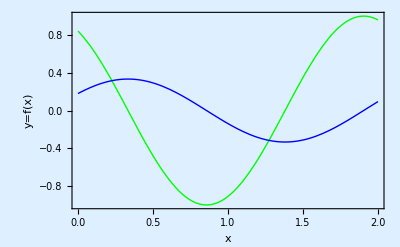

```mathematica
Plot[{f[x],g[x]},{x,0,2}, PlotStyle-> {{Green, Thick},{Blue,Thick}},  AxesLabel-> {"x","y=f(x)"},  Frame->True, Background->LightBlue]
```

```mathematica
(*Zad 2*)
(*PrependTo - na początku i przestaw wartości
AppendTo - na końcu do wartości zmiennej*)
```

```mathematica
Program[lista1_,lista2_]:=Module[{ilosc=0},
If[Length[lista1]≠Length[lista2] , Return ["Błąd"]];

For [it = 1,  it≤Length[lista1],it++,
If[lista1[[it]]≠lista2[[it]],ilosc++];
];
Return [ilosc];
];
```

```mathematica
list1={0,2,5,2,7,34,5,6};
list2={2,15,3,5,7,2,3,6};
Program[list1,list2]
```

6

```mathematica
(*Zad 3*)
Program2[macierz_]:=Module[{iloczyn=1, kolumny},
kolumny=Length[macierz];
For [wiersze = 1,  wiersze≤Length[macierz],wiersze++,
iloczyn=iloczyn*macierz[[wiersze,kolumny]];
kolumny--;
];
Return [iloczyn];
];
```

```mathematica
mac={{2.1,-2,3.3,4},{-0.3,3.1,7.1,-1.2},{-7.2,3.3,11,0.2},{4.1,4.8,-5.2,6.7}};
MatrixForm[mac]
```

(2.1 | -2 | 3.3 | 4
-0.3 | 3.1 | 7.1 | -1.2
-7.2 | 3.3 | 11 | 0.2
4.1 | 4.8 | -5.2 | 6.7)

```mathematica
Program2[mac]
```

384.252